```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/sandrews/SSA/software/Smoldyn/trunk/examples/S7_surfaces/surfacediffuse

```mathematica
timestep=10
diffconst=10
binlow=0
binhigh=100
binwidth=0.5
```

10

10

0

100

0.5

```mathematica
(* Everything below here should take care of itself *)
```

```mathematica
(* Define functions *)
```

```mathematica
gauss[x_,mu_,sigma_]:=1/(sigma*Sqrt[2*Pi])*Exp[-(x-mu)^2/(2*sigma^2)]
```

```mathematica
(* Load and look at data *)
```

```mathematica
simdata=Import["simple2aout.txt"];
```

```mathematica
simdata2=StringReplace[simdata," "->","];
```

```mathematica
simdata3=ImportString[simdata2,"CSV"];
```

```mathematica
simdata4=Drop[simdata3[[1]],1]
```

{0,0,0,249,262,0,0,0,248,0,0,225,0,229,0,233,227,242,249,228,225,262,257,464,261,506,553,494,747,484,730,745,990,733,1027,946,1218,1185,1504,1210,1750,1758,1739,1979,1952,2220,2467,2428,2678,2858,2933,3436,3327,3574,3911,3863,4365,4676,4651,5183,5377,5660,5965,6239,6438,6894,7040,7306,7446,8097,8109,8537,8726,9101,9547,9542,10047,10192,10781,10691,11210,11297,11753,11902,11942,12318,12693,12633,12960,12983,13384,13616,13743,13540,13981,13883,13924,14010,13951,14086,14123,13989,14091,13967,13914,13960,13538,13550,13266,13608,13211,12944,12802,12899,12211,11909,11911,11582,11230,11216,10552,10600,10300,9986,9617,9536,9242,8790,8692,8251,8097,7449,7253,7016,6746,6441,6146,5853,5442,5275,5142,4657,4589,4446,3706,4014,3653,3458,3438,3034,2867,2621,2395,2407,2198,1935,1953,1742,1743,1711,1212,1428,1225,1241,1027,971,720,971,729,758,506,717,477,470,509,248,490,232,232,231,234,225,252,242,241,0,256,0,232,0,0,259,0,0,0,279,247,0,0,0}

```mathematica
nmolec=Total[simdata4]
```

1000000

```mathematica
xvector=Table[i,{i,binlow+binwidth/2,binhigh-binwidth/2,binwidth}];
```

```mathematica
simdata5=Transpose[{xvector,simdata4}];
```

```mathematica
sigma=Sqrt[2*diffconst*timestep]
```

10 √2

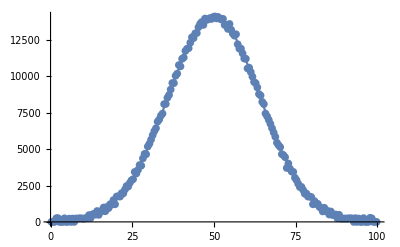

```mathematica
Show[{ListPlot[simdata5],Plot[nmolec*binwidth*gauss[x,50,sigma],{x,binlow,binhigh},PlotRange->All]},PlotRange->All]
```

```mathematica
residuals=Table[simdata4[[i]]-nmolec*binwidth*gauss[xvector[[i]],50,sigma],{i,1,Length[simdata4]}];
```

```mathematica
residuals2=Transpose[{xvector,residuals}];
```

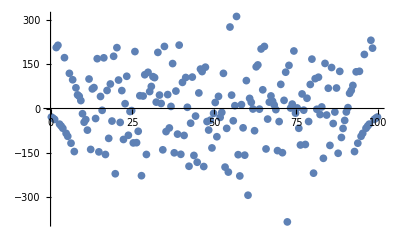

```mathematica
ListPlot[residuals2]
```